## Propagation of errors: implementation

Notebook by Óscar Amaro, February 2023

function getError returns the expression of error propagation for a function F(x1,x2,...) by computing its derivatives. Uncertainties for each variable need also to be specified. See example

```mathematica
Clear[m,V,p,r,T,vars,i,der,arr,Δ,getError,getErrorAuto]

(* get propagation of errors in manually defined variables of expression exp=F(x1,x2,...) *)
getError[exp_,vars_,m_]:=Module[{arrΔ,der,i},

(* array of uncertainties, following same order as variables *)
arrΔ=Array[Δ,Length[vars]];

(* total derivative *)
der = 0;
For[i=1,i<=Length[vars],i++,
der = der+(Abs[D[exp,vars[[i]]]] arrΔ[[i]])^m;
];
der=der^(1/m);

Return[{vars,der}]
]

(* same as getError, but automatically identify symbolic variables *)
getErrorAuto[exp_,m_]:=Module[{vars,arrΔ,der,i},

(* extract variables, except Global *)
(*vars=DeleteDuplicates@Cases[exp,_Symbol,Infinity];*)
vars=With[{globalQ=Context@#==="Global`"&},DeleteDuplicates@Cases[exp,_Symbol?globalQ,Infinity]];

(* array of uncertainties, following same order as variables *)
arrΔ=Array[Δ,Length[vars]];

(* total derivative *)
der = 0;
For[i=1,i<=Length[vars],i++,
der = der+(Abs[D[exp,vars[[i]]]] arrΔ[[i]])^m;
];
der=der^(1/m);

Return[{vars,der}]
]
```

```mathematica
(* example: period of oscillation of a simple pendulum *)
Clear[g,l,T]
Solve[T==2π Sqrt[l/g],g][[1,1]]
(* variables *)
getError[(4 l π^2)/T^2,{l,T},2]
getError[(4 l π^2)/T^2,{l,T},2][[1]]
(* evaluating the propagated error *)
getError[(4 l π^2)/T^2,{l,T},2][[2]]/.{l->1210.2 10^-3,Δ[1]->0.5 10^-3,T->2.21,Δ[2]->0.08}
```

Solve::nongen: Solutions may not be valid for all values of parameters.

g→(4 l π^2)/T^2

{{l,T},√((16 π^4 Δ[1]^2)/Abs[T]^4+64 π^4 Abs[l/T^3]^2 Δ[2]^2)}

{l,T}

0.708218

```mathematica
(4m V)/(p r^4 T^2)/.{m->20.30 10^-3,Δ[1]->0.05 10^-3,V->17 10^-6,Δ[2]->1 10^-6,p->10^5,Δ[3]->0,r->25.60/2 10^-3,Δ[4]->0.05/2 10^-3,T->19 10^-3,Δ[5]->1 10^-3}
getError[(4m V)/(p r^4 T^2),{m,V,p,r,T},1][[2]]/.{m->20.30 10^-3,Δ[1]->0.05 10^-3,V->17 10^-6,Δ[2]->1 10^-6,p->10^5,Δ[3]->0,r->25.60/2 10^-3,Δ[4]->0.05/2 10^-3,T->19 10^-3,Δ[5]->1 10^-3}
```

1.42448

0.248376

## Propagation of errors: example with artificial data for g constant

9.78211

0.717973

0.71019

1.08403

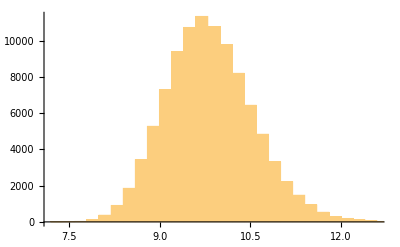

```mathematica
Clear[Nsmpl,ldist,Tdist,gdist,σ1,σ2]
(* number of data points *)
Nsmpl=10^5;

(* example of expression for typical values*)
(4 l π^2)/T^2/.{l->1.2102,T->2.21}

(* generate Gaussian data *)
ldist =RandomVariate[NormalDistribution[1.2102,0.5 10^-3],{Nsmpl}];
Tdist =RandomVariate[NormalDistribution[2.21,0.08],{Nsmpl}];
(* check that Mean and StandardDeviation give the expected results *)
StandardDeviation[ldist];

(* generate output distribution from the Gaussian input *)
gdist=(4 l π^2)/T^2/.{l->ldist,T->Tdist};

(* standard deviation of output from data *)
σ1=StandardDeviation[gdist]
(* standard deviation of output from "propagation error" *)
σ2=getError[(4 l π^2)/T^2,{l,T},2][[2]]/.{Δ[1]->StandardDeviation[ldist],Δ[2]->StandardDeviation[Tdist],l->Mean[ldist],T->Mean[Tdist]}
(* percentage error of "propagation error" approach *)
Abs[σ2-σ1]/σ1*100

Histogram[gdist]
```